# Magnetic Resonance Design Experiment

```mathematica
(*$Path=Append[$Path,"PATH_TO_SpinDynamica"];*)
$Path=Append[$Path,"/Users/kis/KIS Dropbox/Kushal Seetharam/NMR QSim/Code/ZULF/Mathematica/SDv3.10.2/SpinDynamica"];
Quiet[Needs["SpinDynamica`"];]
```

SpinDynamica version SDv3.10.2 loaded by Mathematica 14.3 running on Mac OS X ARM (64-bit).

## High field polarization

```mathematica
Quiet[SetSpinSystem[2]];
Quiet[SetBasis[ZeemanBasis[]]];
Quiet[SetOperatorBasis[CartesianProductOperatorBasis[]]]
```

```mathematica
ρHF=Quiet[ThermalEquilibriumDensityOperator[-(γC*opI[1,"z"]+γH*opI[2,"z"])B0,temp]]
```

1/4 (-(B0 ℏ (-γC I_(1z)-γH I_(2z)))/(kB temp)+𝟙)

```mathematica
BasisKets[]
```

{|αα⟩,|βα⟩,|αβ⟩,|ββ⟩}

```mathematica
paramsHF={γC->Quantity[GyromagneticRatio[13],"Hertz"/"Teslas"],γH->Quantity[GyromagneticRatio[1],"Hertz"/"Teslas"],kB->Quantity["BoltzmannConstant"],ℏ->Quantity["ReducedPlanckConstant"],temp->Quantity[300,"Kelvins"],J->30,B0->Quantity[1,"Teslas"]};
Table[{BasisKets[][[n]],FullSimplify[OperatorAmplitude[ρHF,BasisKets[][[n]].BasisBras[][[n]]]]-1},{n,1,Length[BasisKets[]]}]/.paramsHF(*δ and ϵ populations*)
```

{{|αα⟩,4.26218×10^-6},{|βα⟩,2.54911×10^-6},{|αβ⟩,-2.54914×10^-6},{|ββ⟩,-4.26221×10^-6}}

```mathematica
H=-(γC*opI[1,"z"]+γH*opI[2,"z"])B0+2π*J*opI[1].opI[2];
```

## Relaxation due to Dipolar Interaction

```mathematica
Clear[τC,rCH,ωDD]
```

```mathematica
τC=100*10^-12;
rCH = 1.1 10^-10;
```

```mathematica
ωDD[i_,j_]:=DirectDipolarCoupling[IsotopicType[[i]],IsotopicType[[j]],RR[i,j]];
```

```mathematica
IsotopicType={13,1};
coordinates = {{0,0,0},{rCH,0,0}};
RR[j_,k_]:=Distance[coordinates⟦j⟧,coordinates⟦k⟧]
ΩDDPR[j_,k_]:=AxesToEuler[AxisSystem[coordinates⟦k⟧-coordinates⟦j⟧],AxisSystem[-ez]]
ΓDDterm[{i_,j_},{k_,l_}]:=
-6/5 ωDD[i,j]ωDD[k,l](
Sum[τC*WignerD[2,{0,m1}][ΩDDPR[i,j]]Conjugate[WignerD[2,{0,m1}][ΩDDPR[k,l]]],
{m1,-2,2}]Sum[(-1)^m DoubleCommutationSuperoperator[opT[{i,j},{2,m}],opT[{k,l},{2,-m}]],
{m,-2,2}])
ΓDD = Quiet[Superoperator[ΓDDterm[{1,2},{1,2}]]];
```

For ?WignerD click <here>

## Build full evolution matrix

```mathematica
relaxmat=Chop[FullSimplify[Table[LiouvilleBracket[BasisOperators[][[n]],ΓDD,BasisOperators[][[m]]]/LiouvilleBracket[BasisOperators[][[m]],BasisOperators[][[m]]],{n,1,16,1},{m,1,16,1}]]];
```

```mathematica
H0mat=Chop[FullSimplify[Table[LiouvilleBracket[BasisOperators[][[n]],CommutationSuperoperator[H],BasisOperators[][[m]]]/LiouvilleBracket[BasisOperators[][[m]],BasisOperators[][[m]]],{n,1,16,1},{m,1,16,1}]]]/.paramsHF;
Hcmat[τ_]:=Chop[FullSimplify[Table[LiouvilleBracket[BasisOperators[][[n]],CommutationSuperoperator[B1(γC*opI[1,"x"]+γH*opI[2,"x"])τ],BasisOperators[][[m]]]/LiouvilleBracket[BasisOperators[][[m]],BasisOperators[][[m]]],{n,1,16,1},{m,1,16,1}]]]/.paramsHF/.{B1->0*10^-3};
```

```mathematica
QuantityMagnitude[(ⅈ*H0mat+ⅈ*Hcmat[τ]+relaxmat)/.paramsHF]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2.03387 | -6.72828×10^7+0. ⅈ | 0 | -1.01694 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 30 π | 0 | -30 π | 0
0 | 6.72828×10^7+0. ⅈ | -2.03387 | 0.+0. ⅈ | 0 | -1.01694 | 0 | 0 | 0 | -30 π | 0 | 0 | 0 | 30 π | 0 | 0
0 | 0 | 0.+0. ⅈ | -2.03387 | 0 | 0 | -1.01694 | 0 | 30 π | 0 | -30 π | 0 | 0 | 0 | 0 | 0
0 | -1.01694 | 0 | 0 | -2.03387 | -2.67522×10^8+0. ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | -30 π | 0 | 30 π | 0
0 | 0 | -1.01694 | 0 | 2.67522×10^8+0. ⅈ | -2.03387 | 0.+0. ⅈ | 0 | 0 | 30 π | 0 | 0 | 0 | -30 π | 0 | 0
0 | 0 | 0 | -1.01694 | 0 | 0.+0. ⅈ | -2.03387 | 0 | -30 π | 0 | 30 π | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.22032 | -2.67522×10^8+0. ⅈ | 0 | -6.72828×10^7+0. ⅈ | 0.610162 | 0 | 0 | 0 | 0.610162
0 | 0 | 0 | -30 π | 0 | 0 | 30 π | 2.67522×10^8+0. ⅈ | -1.42371 | 0.+0. ⅈ | -0.406775 | -6.72828×10^7+0. ⅈ | 0 | 0 | 0 | 0
0 | 0 | 30 π | 0 | 0 | -30 π | 0 | 0 | 0.+0. ⅈ | -1.42371 | 0 | 0 | -6.72828×10^7+0. ⅈ | -0.406775 | 0 | 0
0 | 0 | 0 | 30 π | 0 | 0 | -30 π | 6.72828×10^7+0. ⅈ | -0.406775 | 0 | -1.42371 | -2.67522×10^8+0. ⅈ | 0 | 0.+0. ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.610162 | 6.72828×10^7+0. ⅈ | 0 | 2.67522×10^8+0. ⅈ | -1.22032 | 0.+0. ⅈ | 0 | 0.+0. ⅈ | 0.610162
0 | -30 π | 0 | 0 | 30 π | 0 | 0 | 0 | 0 | 6.72828×10^7+0. ⅈ | 0 | 0.+0. ⅈ | -1.42371 | 0 | -0.406775 | 0.+0. ⅈ
0 | 0 | -30 π | 0 | 0 | 30 π | 0 | 0 | 0 | -0.406775 | 0.+0. ⅈ | 0 | 0 | -1.42371 | -2.67522×10^8+0. ⅈ | 0
0 | 30 π | 0 | 0 | -30 π | 0 | 0 | 0 | 0 | 0 | 0 | 0.+0. ⅈ | -0.406775 | 2.67522×10^8+0. ⅈ | -1.42371 | 0.+0. ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.610162 | 0 | 0 | 0 | 0.610162 | 0.+0. ⅈ | 0 | 0.+0. ⅈ | -1.22032)

## Define equilibrium and initial operator

```mathematica
ρeq=QuantityMagnitude[Table[OperatorAmplitude[BasisOperators[][[n]]][ρHF],{n,1,16,1}]/.paramsHF]
ρ1=QuantityMagnitude[Table[OperatorAmplitude[BasisOperators[][[n]]][RotationSuperoperator[{π,"y"}][ρHF]],{n,1,16,1}]/.paramsHF]
ρ[t_]:={a1[t],a2[t],a3[t],a4[t],a5[t],a6[t],a7[t],a8[t],a9[t],a10[t],a11[t],a12[t],a13[t],a14[t],a15[t],a16[t]}
```

{1/2,0,0,4.28268×10^-7,0,0,1.70283×10^-6,0,0,0,0,0,0,0,0,0}

{1/2,0,0,-4.28268×10^-7,0,0,-1.70283×10^-6,0,0,0,0,0,0,0,0,0}

```mathematica
{1/2,0,0,4.28268317262362*^-7,0,0,1.702830195470438*^-6,0,0,0,0,0,0,0,0,0}
```

{1/2,0,0,4.28268×10^-7,0,0,1.70283×10^-6,0,0,0,0,0,0,0,0,0}

```mathematica
ρHF2=QuantityMagnitude[Table[OperatorAmplitude[BasisOperators[][[n]]][ρHF],{n,1,16,1}]/.paramsHF]
sol=NDSolve[{D[ρ[t],t]==QuantityMagnitude[(ⅈ*H0mat+ⅈ*Hcmat[t]+relaxmat)/.paramsHF].(ρ[t]-ρHF2),ρ[0]==(ρHF2-{0,0,0,2*4.28268317262362*^-7,0,0,0,0,0,0,0,0,0,0,0,0})},ρ[t],{t,0.00,10}];
```

{1/2,0,0,4.28268×10^-7,0,0,1.70283×10^-6,0,0,0,0,0,0,0,0,0}

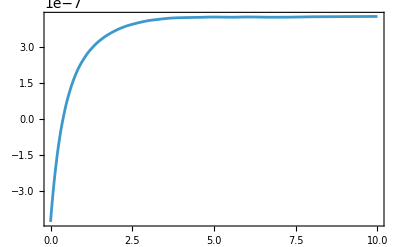

```mathematica
Plot[ρ[t][[4]]/.sol,{t,0,10},PlotRange->All]
```

```mathematica
Mop=(γC*opI[1,"+"]+γH*opI[2,"+"]);(*quadrature operator*)
```

```mathematica
(*Probability of measuring μ characteristic to Mop for time t*)
```

```mathematica
p[μ_,t_]:=NIntegrate[Exp[ⅈ*μ*s]*LiouvilleBracket[ρ[t].MatrixExp[-ⅈ*Mop*s]],{s,-∞,∞}]
```

```mathematica
p[1,1]
(*Plot[p[t]/.sol,{t,0,10},PlotRange->All]*)
```

NIntegrate::inumr: The integrand Cos[s] LiouvilleBracket[{a1[1],a2[1],a3[1],a4[1],a5[1],a6[1],a7[1],a8[1],a9[1],a10[1],a11[1],a12[1],a13[1],a14[1],a15[1],a16[1]}.MatrixExp[«1»]] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[Exp[ⅈ s] LiouvilleBracket[ρ[1].MatrixExp[-ⅈ Mop s]],{s,-∞,∞}]